```mathematica
forces={{1,1},{-1,2},{3,0}};
moments={{0,0,3},{0,0,-2},{0,0,2}};

RenderFBD[forces_,moments_]:=
Module[{},
If[Length[forces[[1]]]<3,
(* 2D *)
forceArrows=Arrow[{{0,0,0},{#1[[1]],#1[[2]],0}}]&/@forces;
momentArrows=Arrow[{{0,0,0},#}]&/@moments;
,
forceArrows=Arrow[{{0,0,0},#}]&/@forces;
momentArrows=Arrow[{{0,0,0},#}]&/@moments;
];
Graphics3D[{Blue,forceArrows,LightBlue,momentArrows}]
];

BuoyObject[shape_,density_]:=
{shape,density};

(*BuoyObject[Tetrahedron[],*)

RenderFBD[forces,moments]
```

-Graphics3D-

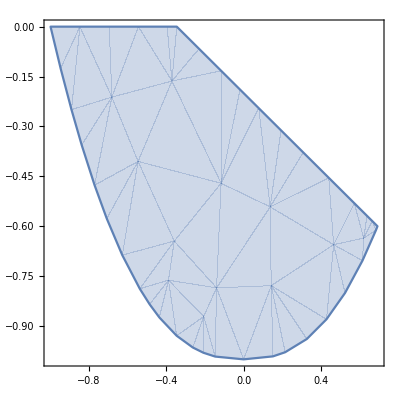

```mathematica
RenderBoat[n:_,θ:_,d:_]:=
Module[{yBounds,y,zBounds,z,boatHull,waterLine,intersects,boatHullRegion,boatHullRegionFunc,region},
boatHull=Abs[y]^n-1;
waterLine=-y*Tan[θ]-d;

intersects=Solve[boatHull==waterLine,Reals];(*InverseFunctions->True];*)

yBounds={Max[-1,y/.intersects[[1]]],Min[1,y/.intersects[[2]]]};
zBounds={boatHull,Min[0,waterLine]};

region=#1[[1]]≤y≤#1[[2]]&&#2[[1]]≤z≤#2[[2]]&@@{yBounds,zBounds};

(*boatHullRegion=ImplicitRegion[region,{y,z}];*)

(*RegionPlot[region,{y,-1,1},{z,-1,1}]*)
(*RegionPlot[boatHullRegion]*)

Show[RegionPlot[region,{y,-1,1},{z,-1,1}],Plot[waterLine,{y,-1,1}],AspectRatio->Automatic]
];

MakeBoatHull[n_,θ_,d_]:=
Module[{},
boatHull=Abs[y]^n-1;
waterLine=-y*Tan[θ]-d;

yBounds={-1,1};
zBounds={boatHull,0};

makeRegion=#1[[1]]≤y≤#1[[2]]&&#2[[1]]≤z≤#2[[2]]&;

boatHullRegion=ImplicitRegion[makeRegion@@{yBounds,zBounds},{y,z}];

waterLineRegion=ImplicitRegion[makeRegion@@{{-2,2},{waterLine,0}},{y,z}];
RegionPlot[RegionDifference[boatHullRegion,waterLineRegion]]
(*wlRegion=ImplicitRegion[,{y,z}];*)

(*RegionIntersection*)
];

MakeBoatHull[2.5,30Degree,0.2]
Manipulate[
MakeBoatHull[n,θ,d],
{{n,2},0,5},{{θ,0},-Pi/2,Pi/2},{d,0,1},
SynchronousUpdating->False]
```

```mathematica
Manipulate[
Module[{x},
Graphics[BezierCurve[points],PlotRange->10]
],
{{points,CirclePoints[7]*10},Locator,LocatorAutoCreate->True}]
```

```mathematica
pts={
{{0,0,0},{0,1,0},{0,2,0},{0,3,0}},
{{1,0,0},{1,1,1},{1,2,1},{1,3,0}},
{{2*2,0,0+1/2},{2,1,1},{2,2,1},{2*2,3,0+1/2}},
{{3,0,0},{3,1,0},{3,2,0},{3,3,0}}
};

bezierPoints=7;
r=10;
boatLength=40;
sectionLength=boatLength/4;

defaultPoints[r_,p_,z_, y_]:={#[[1]],#[[2]]+y,z}&/@CirclePoints[r,p];
pts=Table[defaultPoints[r*(1-(Abs[z]/30)),bezierPoints,z,-z^2/100],{z,-boatLength/2,boatLength/2,sectionLength}];

MatrixForm[N[pts]];


basePoints=Table[{0,-5,z},{z,-boatLength/2,boatLength/2,sectionLength}];
transposedPts=Transpose[pts];
ptsTwo=Transpose[Append[Prepend[transposedPts,basePoints],basePoints]];


pts=Reverse[pts];
N[pts]
(* Actually create the function *)
f=BezierFunction[pts];

(* Render Boat *)
boatPlot=ParametricPlot3D[f[u,v],{u,0,1},{v,0,1},Mesh->Full,PlotPoints->{40, 15}];
(*ParametricPlot[f[u,v]*)
(* Export Boat *)
fileLoc="/home/wolf/qea/hull.stl";
Export[
fileLoc,
boatPlot
];

Import[fileLoc,"BoundaryMeshRegion"]

Show[Graphics3D[{PointSize[Medium],Red,Map[Point,pts]}],
Graphics3D[{Gray,Line[pts],Line[Transpose[pts]]}],boatPlot]
```

{{{1.44628,-7.00323,20.},{3.24976,-4.74174,20.},{2.6061,-1.9217,20.},{0.,-0.666667,20.},{-2.6061,-1.9217,20.},{-3.24976,-4.74174,20.},{-1.44628,-7.00323,20.}},{{2.89256,-7.00646,10.},{6.49952,-2.48347,10.},{5.21221,3.1566,10.},{0.,5.66667,10.},{-5.21221,3.1566,10.},{-6.49952,-2.48347,10.},{-2.89256,-7.00646,10.}},{{4.33884,-9.00969,0.},{9.74928,-2.22521,0.},{7.81831,6.2349,0.},{0.,10.,0.},{-7.81831,6.2349,0.},{-9.74928,-2.22521,0.},{-4.33884,-9.00969,0.}},{{2.89256,-7.00646,-10.},{6.49952,-2.48347,-10.},{5.21221,3.1566,-10.},{0.,5.66667,-10.},{-5.21221,3.1566,-10.},{-6.49952,-2.48347,-10.},{-2.89256,-7.00646,-10.}},{{1.44628,-7.00323,-20.},{3.24976,-4.74174,-20.},{2.6061,-1.9217,-20.},{0.,-0.666667,-20.},{-2.6061,-1.9217,-20.},{-3.24976,-4.74174,-20.},{-1.44628,-7.00323,-20.}}}

BoundaryMeshRegion::binsect: The boundary curves self-intersect or cross each other in BoundaryMeshRegion[{{1.87798,-6.48664,19.4872},{1.59442,-7.01105,18.9744},{2.24456,-5.91198,18.9744},«46»,{2.36979,2.29142,2.5641},«2333»},{{},{},{Polygon[{{1,2,3},{6,7,8},«48»,«4568»}]}}].

$Failed

-Graphics3D-

```mathematica
inertialMoment[reg_?RegionQ,axis_InfiniteLine]:=Module[{df=RegionDistance[axis]},Integrate[df[{x,y,z}],{x,y,z}∈reg]]

com[reg_?RegionQ]:=
Module[{dens=1},
Integrate[dens*{x,y,z},{x,y,z}∈reg]/
Integrate[dens,{x,y,z}∈reg]]

mr=Import["/home/wolf/qea/scad-hull.stl"]
mer=Import["/home/wolf/qea/example007.stl"]

(*mr=ConvexHullMesh[RandomReal[1,{30,3}]];*)
axis=InfiniteLine[{1,0,0},{1,2,3}];
Show[Graphics3D[{Red,Thick,axis},Boxed->False],HighlightMesh[mr,{Style[2,Opacity[0.25]]}],Graphics3D[{Blue,Thick,Point[com[mr]]}]]
inertialMoment[mr,axis]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

65.6474

```mathematica
Import["/home/wolf/qea/hull.stl"]
```

-Graphics3D-